Electron–positron pairs beaming in the Breit–Wheeler process

X Ribeyre, E d’Humières, O Jansen, S Jequier and V T Tikhonchuk, Plasma Phys. Control. Fusion 59 (2017) 014024
Notebook: Óscar Amaro, October 2022 @ GoLP-EPP
Contact: oscar.amaro@tecnico.ulisboa.pt

Introduction
In this notebook we reproduce some results from the paper.

Here we reproduce figures 2, 3 and 7. All figures show two cases: Eγ1=Eγ2=4 or Eγ1=4, Eγ2=10.

## Geometry

Primed values are from CM frame, unprimed from lab frame.

```mathematica
Clear[c,me,pγ1,pγ2,Eγ1,Eγ2,pγ1v,pγ2v,θcm,θp,Ecm,θpbeam,θe,Emax,Emin,Ee,θebeam]
c=me=1;
(* photon momenta, by definition *)
pγ1=Eγ1/c;
pγ2=Eγ2/c;
(* photon momenta according to Figure 1 geometry *)
pγ1v={pγ1 Cos[θp/2],-pγ1 Sin[θp/2],0};
pγ2v={pγ2 Cos[θp/2],pγ2 Sin[θp/2],0};

(* equation 1 *)
βcm=(pγ1v+pγ2v)/(Eγ1+Eγ2);

(* prove eq 2 *)
Refine[Norm[βcm]^2,{Eγ1>0,Eγ2>0,θp>0}]//Simplify

(* prove eq 3 *)
(* θcm is angle between pγ1 and βcm (the latter being along x axis) *)
Refine[Refine[Tan[Refine[ArcCos[(pγ1v.βcm)/(pγ1 Norm[βcm])]//Simplify,{Eγ1>0,Eγ2>0,θp>0}]//Simplify],{Eγ1>0,Eγ2>0,θp>0}]^2//Simplify//Sqrt,{Eγ1>0,Eγ2>0,θp>0,Eγ1+Eγ2 Cos[θp]>0,Sin[θp]>0}]

(* prove eq 4 *)
(Eγ1^2 + 2pγ1v.pγ2v+Eγ2^2)-(Eγ1+Eγ2)^2//Simplify//TrigReduce//Simplify
Ecm=Sqrt[-2 Eγ1 Eγ2 (-1+Cos[θp])];

γcm=Refine[1/Sqrt[1-Norm[βcm]^2],{θp>0}]
Eeprime=Ecm/2;
peprime=Sqrt[Ecm^2/4-1];
(* equation 7 *)
pepll=γcm(peprime Cos[θprime]+Norm[βcm] Eeprime)//Simplify;
θpbeam=ArcCos[1-(Eγ1+Eγ2)/(Eγ1 Eγ2)];

(* get θp @ pe|| has imaginary component *)
Solve[-2+Eγ1 Eγ2-Eγ1 Eγ2 Cos[θp]==0,θp];

(* equation 7 *)
θebeam=Refine[ArcTan[peprime/(γcm(Norm[βcm]^2 Eeprime^2-peprime^2))]//Simplify,{Eγ1>0,Eγ2>0,θp ∈Reals}]//Simplify

(* don't use equation 14, use equation 6 *)
Ee=(γcm (Eeprime+Norm[βcm] peprime Cos[θprime]))//Simplify;
(*Emax=(Eγ1+Eγ2)/2+(Sqrt[(Eγ1-Eγ2)^2-Ecm^2]Sqrt[Ecm^2-4])/(2Ecm);*)
(*Emin=(Eγ1+Eγ2)/2-(Sqrt[(Eγ1-Eγ2)^2-Ecm^2]Sqrt[Ecm^2-4])/(2Ecm);*)
```

(Eγ1^2+Eγ2^2+2 Eγ1 Eγ2 Cos[θp])/(Eγ1+Eγ2)^2

(Eγ2 Sin[θp])/(Eγ1+Eγ2 Cos[θp])

2 Eγ1 Eγ2 (-1+Cos[θp])

1/(√(1-Abs[(Eγ1 Cos[θp/2]+Eγ2 Cos[θp/2])/(Eγ1+Eγ2)]^2-Abs[(-Eγ1 Sin[θp/2]+Eγ2 Sin[θp/2])/(Eγ1+Eγ2)]^2))

ArcTan[(2 (Eγ1+Eγ2)^2 √(-(Eγ1 Eγ2 (-1+Cos[θp]))/(Eγ1+Eγ2)^2) √(-2+Eγ1 Eγ2-Eγ1 Eγ2 Cos[θp]))/(2 Eγ1^2+4 Eγ1 Eγ2+2 Eγ2^2-3 Eγ1^2 Eγ2^2+4 Eγ1^2 Eγ2^2 Cos[θp]-Eγ1^2 Eγ2^2 Cos[2 θp])]

## Figure 2: pe|| in lab frame (eq.7)

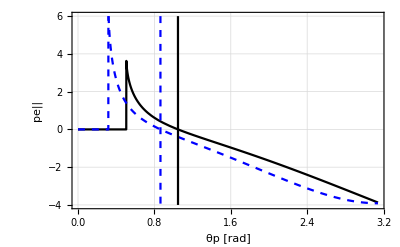

```mathematica
Plot[{(HeavisideTheta[θp-ArcCos[(-2+Eγ1 Eγ2)/(Eγ1 Eγ2)]])pepll/.{Eγ1->4,Eγ2->4,θprime->π},(HeavisideTheta[θp-ArcCos[(-2+Eγ1 Eγ2)/(Eγ1 Eγ2)]])pepll/.{Eγ1->4,Eγ2->10,θprime->π},(20HeavisideTheta[θpbeam-θp]-10)/.{Eγ1->4,Eγ2->4,θprime->π},(20HeavisideTheta[θpbeam-θp]-10)/.{Eγ1->4,Eγ2->10,θprime->π}},{θp,0,π},PlotRange->{-4,6},GridLines->Automatic,Frame->True,FrameLabel->{"θp [rad]","pe||"},PlotStyle->{Black, Directive[Blue,Dashed],Black, Directive[Blue,Dashed]},Filling->None]
```

## Figure 3: θe,beam (eq.11)

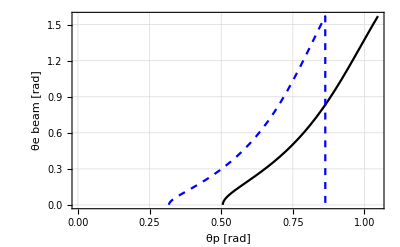

```mathematica
Plot[{θebeam/.{Eγ1->4,Eγ2->4,θprime->π
},θebeam/.{Eγ1->4,Eγ2->10,θprime->π}},{θp,0,π/3},PlotRange->{{0,π/3},{0,π/2}},GridLines->Automatic,Frame->True,FrameLabel->{"θp [rad]","θe beam [rad]"},PlotStyle->{Black, Directive[Blue,Dashed]},Filling->None]
```

## Figure 7: Maximum and minimum energies (eq.6)

bandwidth is maximum for θp=θp,beam
vertical line given by equation 10 θp,beam

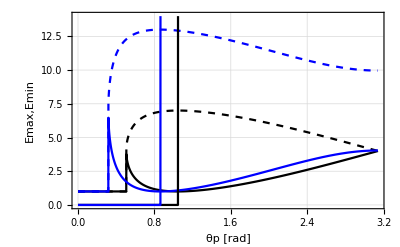

```mathematica
Plot[{(HeavisideTheta[ArcCos[(-2+Eγ1 Eγ2)/(Eγ1 Eγ2)]-θp]+HeavisideTheta[θp-ArcCos[(-2+Eγ1 Eγ2)/(Eγ1 Eγ2)]]Ee)/.{Eγ1->4,Eγ2->4,θprime->π},(HeavisideTheta[ArcCos[(-2+Eγ1 Eγ2)/(Eγ1 Eγ2)]-θp]+HeavisideTheta[θp-ArcCos[(-2+Eγ1 Eγ2)/(Eγ1 Eγ2)]]Ee)/.{Eγ1->4,Eγ2->4,θprime->0},(HeavisideTheta[ArcCos[(-2+Eγ1 Eγ2)/(Eγ1 Eγ2)]-θp]+HeavisideTheta[θp-ArcCos[(-2+Eγ1 Eγ2)/(Eγ1 Eγ2)]]Ee)/.{Eγ1->10,Eγ2->4,θprime->π},(HeavisideTheta[ArcCos[(-2+Eγ1 Eγ2)/(Eγ1 Eγ2)]-θp]+HeavisideTheta[θp-ArcCos[(-2+Eγ1 Eγ2)/(Eγ1 Eγ2)]]Ee)/.{Eγ1->10,Eγ2->4,θprime->0},(20HeavisideTheta[θp-ArcCos[1-(Eγ1+Eγ2)/(Eγ1 Eγ2)]])/.{Eγ1->4,Eγ2->4,θprime->π},(20HeavisideTheta[θp-ArcCos[1-(Eγ1+Eγ2)/(Eγ1 Eγ2)]])/.{Eγ1->4,Eγ2->10,θprime->π}},{θp,0,π},PlotRange->{{0,π},{0,14}},GridLines->Automatic,Frame->True,FrameLabel->{"θp [rad]","Emax,Emin"},PlotStyle->{Black, Directive[Black,Dashed],Blue, Directive[Blue,Dashed],Black,Blue},Filling->None]
```

## Figure 5

```mathematica
Clear[Nsmpl,glst,norms]
Nsmpl=10^4;
glst=RandomVariate[NormalDistribution[],{Nsmpl,3}];
norms=ParallelTable[Norm[glst[[i]]],{i,1,Length[glst]}];
glst=glst/norms;
ListPointPlot3D[glst,AspectRatio->1]
```

-Graphics3D-